```mathematica
Integrate[Exp[-(r^2+(0.5*g*t^2-l)^2)/(t^2*v0^2)]/t^4,{t,0,Infinity}]
```

ConditionalExpression[(0.443113 ⅇ^((1. g l)/v0^2-(1. √(g^2/v0^2))/(√(v0^2/(1. l^2+1. r^2)))) v0^2 (√(g^2/v0^2)+1. √(v0^2/(1. l^2+1. r^2))))/(1. l^2+1. r^2),Re[g^2/v0^2]>0&&Re[(1. l^2+1. r^2)/v0^2]>0]

```mathematica
Integrate[(ⅇ^((-0.5 l^2+0.5 g l t-0.125 g^2 t^2-0.5 y^2)/(k m t^2 T)) (1.2533141373155001 l+0.6266570686577501 g t^2))/(t^4 √(1/(k m t^2 T))),{y,0
```

```mathematica
Integrate[Exp[-(x^2)/(t^2*2*m*k*T)],{x,-Infinity,Infinity}]
```

ConditionalExpression[(√(2 π))/(√(1/(k m t^2 T))),Re[1/(k m t^2 T)]>0]

```mathematica
*(0.5*g*t^2+l)
```

```mathematica
Integrate[Exp[-(r^2+(0.5*g*t^2-l)^2)/(t^2*v0^2)]/t^2,{t,0,Infinity}]
```

```mathematica
Integrate[Exp[-((0.5*g*t^2-l+dv*t)^2)/(t^2*v^2)]/t^4,{t,0,Infinity}]
Integrate[Exp[-((0.5*g*t^2-l+dv*t)^2)/(t^2*v^2)]/t^2,{t,0,Infinity}]
```

∫_0^∞ (ⅇ^(-((-l+dv t+0.5 g t^2)^2)/(t^2 v^2)))/t^4 ⅆt

∫_0^∞ (ⅇ^(-((-l+dv t+0.5 g t^2)^2)/(t^2 v^2)))/t^2 ⅆt

```mathematica
FullSimplify[((0.44311346272637897 ⅇ^((1. g l)/v0^2-(1. √(g^2/v0^2))/(√(v0^2/(1. l^2+1. r^2)))) v0^2 (√(g^2/v0^2)+1. √(v0^2/(1. l^2+1. r^2))))/(1. l^2+1. r^2))*l+(0.8862269254527579 ⅇ^((1. g l)/v0^2-(1. √(g^2/v0^2))/(√(v0^2/(1. l^2+1. r^2)))) √(v0^2/(1. l^2+1. r^2)))*1/2*g]
```

(ⅇ^((1. g l)/v0^2-(1. √(g^2/v0^2))/(√(v0^2/(1. l^2+1. r^2)))) (0.443113 g l^2 √(v0^2/(1. l^2+1. r^2))+0.443113 g r^2 √(v0^2/(1. l^2+1. r^2))+0.443113 l v0^2 (1. √(g^2/v0^2)+1. √(v0^2/(1. l^2+1. r^2)))))/(1. l^2+1. r^2)

```mathematica
N[Sqrt[Pi]/4]
```

0.443113

```mathematica
FullSimplify[(g*r^2+g*l*r+v^2*l)/r^3]
```

(g r (l+r)+l v^2)/r^3

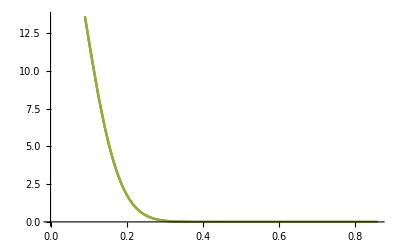

```mathematica
g0=9.81;
l0=0.8587;
v0=0.3;
Plot[{Exp[g0*l0/(v0^2)]*Exp[-g0*Sqrt[x^2+l0^2]/v0^2]*(Sqrt[x^2+l0^2]^2*g0+g0*l0*Sqrt[x^2+l0^2]+v0^2*l0)/Sqrt[x^2+l0^2]^3,Exp[g0*l0/(v0^2)]*Exp[-g0*x^2/(2*l0*v0^2)]*Exp[-g0*Sqrt[l0^2]/v0^2]*(Sqrt[l0^2]^2*g0+g0*l0*Sqrt[l0^2]+v0^2*l0)/Sqrt[l0^2]^3,Exp[g0*l0/(v0^2)]*Exp[-g0*x^2/(2*l0*v0^2)]*Exp[-g0*Sqrt[l0^2]/v0^2]*(Sqrt[l0^2]^2*g0+g0*l0*Sqrt[l0^2])/Sqrt[l0^2]^3},{x,0,l0}]
```

```mathematica
Sqrt[l0*g0/2]/3
```

0.684099

```mathematica
Integrate[{Exp[-g*Sqrt[x^2+l^2]/v^2]*(Sqrt[x^2+l^2]^2*g+g*l*Sqrt[x^2+l^2]+v^2*l2)/Sqrt[x^2+l^2]^3},{x,-Infinity,Infinity}]
```

$Aborted

```mathematica
Integrate[Exp[-g*r/v^2]/r^3,r]
```

ⅇ^(-(g r)/v^2) (-1/(2 r^2)+g/(2 r v^2))+(g^2 ExpIntegralEi[-(g r)/v^2])/(2 v^4)

```mathematica
Integrate[PolyLog[3/2,Exp[-x^2]],x]
```

∫PolyLog[3/2,ⅇ^(-x^2)]ⅆx

```mathematica
Integrate[Exp[-x^2*k/(2*σ^2)],{x,-Infinity,Infinity}]
```

ConditionalExpression[(√(2 π))/(√(k/σ^2)),Re[k/σ^2]>0]

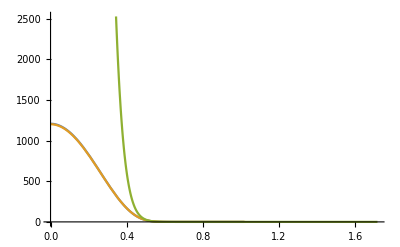

```mathematica
g0=9.81;
l0=0.8587;
v0=Sqrt[l0*g0/2]/12;
η=10000;
Plot[{-2*g0*l0^2*PolyLog[5/2,-η*Exp[-x^2/v0^2]]-v0^2*l0*PolyLog[7/2,-η*Exp[-x^2/v0^2]],-2*g0*l0^2*PolyLog[5/2,-η*Exp[-x^2/v0^2]],2*g0*l0^2*η*Exp[-x^2/v0^2]},{x,0,2*l0}]
```

```mathematica
v0
```

0.256537

```mathematica
0.5*0.37
```

0.185

```mathematica
Integrate[Integrate[1-1/R^2*(x^2/η0^2+y^2+(z0-1/2*g*t^2)),{x,-R*Sqrt[η0-y^2-(z0-1/2*g*t^2)],R*Sqrt[η0-y^2-(z0-1/2*g*t^2)]}],{y,-R*Sqrt[1-(z0-1/2*g*t^2)],R*Sqrt[1-(z0-1/2*g*t^2)]}]
```

ConditionalExpression[1/(6 R η0^2)(3/8 π (g t^2-2 z0+2 η0) (-2 η0^2 (3 z0+η0)-g t^2 (R^2-3 η0^2)+2 R^2 (z0+η0 (-1+4 η0)))+3/8 π √(-1/(√(g t^2-2 z0+2 η0))) √(-√(g t^2-2 z0+2 η0)) (g t^2-2 z0+2 η0) (-2 η0^2 (3 z0+η0)-g t^2 (R^2-3 η0^2)+2 R^2 (z0+η0 (-1+4 η0)))-1/(8 √(2-(2 R^2 (2+g t^2-2 z0))/(g t^2-2 z0+2 η0)))√(g t^2-R^2 (2+g t^2-2 z0)-2 z0+2 η0) (-2 R √(1+(g t^2)/2-z0) √((g t^2-R^2 (2+g t^2-2 z0)-2 z0+2 η0)/(g t^2-2 z0+2 η0)) (2 R^4 (2+g t^2-2 z0)+3 η0^2 (5 g t^2+2 (-5 z0+η0))+R^2 (2 η0 (-5+6 η0)-g t^2 (5+6 η0^2)+2 z0 (5+6 η0^2)))-3 √(2 g t^2-4 z0+4 η0) (-2 η0^2 (3 z0+η0)-g t^2 (R^2-3 η0^2)+2 R^2 (z0+η0 (-1+4 η0))) ArcSin[(R √(2+g t^2-2 z0))/(√(g t^2-2 z0+2 η0))])+1/(8 √(2-(2 R^2 (2+g t^2-2 z0))/(g t^2-2 z0+2 η0)))√(g t^2-R^2 (2+g t^2-2 z0)-2 z0+2 η0) (2 R √(1+(g t^2)/2-z0) √((g t^2-R^2 (2+g t^2-2 z0)-2 z0+2 η0)/(g t^2-2 z0+2 η0)) (2 R^4 (2+g t^2-2 z0)+3 η0^2 (5 g t^2+2 (-5 z0+η0))+R^2 (2 η0 (-5+6 η0)-g t^2 (5+6 η0^2)+2 z0 (5+6 η0^2)))+3 √(2 g t^2-4 z0+4 η0) (-2 η0^2 (3 z0+η0)-g t^2 (R^2-3 η0^2)+2 R^2 (z0+η0 (-1+4 η0))) ArcSin[(R √(2+g t^2-2 z0))/(√(g t^2-2 z0+2 η0))])),Re[(√(2 g t^2-4 z0+4 η0))/(R √(2+g t^2-2 z0))]>√2||√2+Re[(√(2 g t^2-4 z0+4 η0))/(R √(2+g t^2-2 z0))]<0||(√(g t^2-2 z0+2 η0))/(R √(2+g t^2-2 z0))∉ℝ]

```mathematica
FullSimplify[1/(6 R η0^2)(3/8 π (g t^2-2 z0+2 η0) (-2 η0^2 (3 z0+η0)-g t^2 (R^2-3 η0^2)+2 R^2 (z0+η0 (-1+4 η0)))+3/8 π √(-1/(√(g t^2-2 z0+2 η0))) √(-√(g t^2-2 z0+2 η0)) (g t^2-2 z0+2 η0) (-2 η0^2 (3 z0+η0)-g t^2 (R^2-3 η0^2)+2 R^2 (z0+η0 (-1+4 η0)))-1/(8 √(2-(2 R^2 (2+g t^2-2 z0))/(g t^2-2 z0+2 η0)))√(g t^2-R^2 (2+g t^2-2 z0)-2 z0+2 η0) (-2 R √(1+(g t^2)/2-z0) √((g t^2-R^2 (2+g t^2-2 z0)-2 z0+2 η0)/(g t^2-2 z0+2 η0)) (2 R^4 (2+g t^2-2 z0)+3 η0^2 (5 g t^2+2 (-5 z0+η0))+R^2 (2 η0 (-5+6 η0)-g t^2 (5+6 η0^2)+2 z0 (5+6 η0^2)))-3 √(2 g t^2-4 z0+4 η0) (-2 η0^2 (3 z0+η0)-g t^2 (R^2-3 η0^2)+2 R^2 (z0+η0 (-1+4 η0))) ArcSin[(R √(2+g t^2-2 z0))/(√(g t^2-2 z0+2 η0))])+1/(8 √(2-(2 R^2 (2+g t^2-2 z0))/(g t^2-2 z0+2 η0)))√(g t^2-R^2 (2+g t^2-2 z0)-2 z0+2 η0) (2 R √(1+(g t^2)/2-z0) √((g t^2-R^2 (2+g t^2-2 z0)-2 z0+2 η0)/(g t^2-2 z0+2 η0)) (2 R^4 (2+g t^2-2 z0)+3 η0^2 (5 g t^2+2 (-5 z0+η0))+R^2 (2 η0 (-5+6 η0)-g t^2 (5+6 η0^2)+2 z0 (5+6 η0^2)))+3 √(2 g t^2-4 z0+4 η0) (-2 η0^2 (3 z0+η0)-g t^2 (R^2-3 η0^2)+2 R^2 (z0+η0 (-1+4 η0))) ArcSin[(R √(2+g t^2-2 z0))/(√(g t^2-2 z0+2 η0))]))]
```

$Aborted

```mathematica
Integrate[Integrate[1-1/R^2*(x^2/η0^2+y^2+z^2),{x,-R*Sqrt[η0-y^2-z^2],R*Sqrt[η0-y^2-z^2]}],{y,-R*Sqrt[1-z^2],R*Sqrt[1-z^2]}]
```

ConditionalExpression[1/(3 R η0^2)2 (3/8 π (z^2-η0) (η0^2 (3 z^2+η0)+R^2 (-z^2+η0-4 η0^2))+3/16 π (z^2-η0) √(-1/(√(-z^2+η0))) √(-√(-z^2+η0)) (η0^2 (3 z^2+η0)+R^2 (-z^2+η0-4 η0^2))-3/16 π √(-1/(√(-z^2+η0))) √(-√(-z^2+η0)) (-z^2+η0) (η0^2 (3 z^2+η0)+R^2 (-z^2+η0-4 η0^2))+1/8 √(-z^2+R^2 (-1+z^2)+η0) (3 R √(1-z^2) η0^2 (-5 z^2+2 R^2 (-1+z^2)+η0)+R^3 √(1-z^2) (5 z^2-2 R^2 (-1+z^2)+η0 (-5+12 η0))-(3 √(-z^2+η0) (η0^2 (3 z^2+η0)+R^2 (-z^2+η0-4 η0^2)) ArcSin[(R √(1-z^2))/(√(-z^2+η0))])/(√((R^2+z^2-R^2 z^2-η0)/(z^2-η0))))-1/8 √(-z^2+R^2 (-1+z^2)+η0) (-3 R √(1-z^2) η0^2 (-5 z^2+2 R^2 (-1+z^2)+η0)-R^3 √(1-z^2) (5 z^2-2 R^2 (-1+z^2)+η0 (-5+12 η0))+(3 √(-z^2+η0) (η0^2 (3 z^2+η0)+R^2 (-z^2+η0-4 η0^2)) ArcSin[(R √(1-z^2))/(√(-z^2+η0))])/(√((R^2+z^2-R^2 z^2-η0)/(z^2-η0))))),Re[(√(-z^2+η0))/(R √(1-z^2))]>1||Re[(√(-z^2+η0))/(R √(1-z^2))]<-1||(√(-z^2+η0))/(R √(1-z^2))∉ℝ]

```mathematica
Simplify[1/(3 R η0^2)2 (3/8 π (z^2-η0) (η0^2 (3 z^2+η0)+R^2 (-z^2+η0-4 η0^2))+3/16 π (z^2-η0) √(-1/(√(-z^2+η0))) √(-√(-z^2+η0)) (η0^2 (3 z^2+η0)+R^2 (-z^2+η0-4 η0^2))-3/16 π √(-1/(√(-z^2+η0))) √(-√(-z^2+η0)) (-z^2+η0) (η0^2 (3 z^2+η0)+R^2 (-z^2+η0-4 η0^2))+1/8 √(-z^2+R^2 (-1+z^2)+η0) (3 R √(1-z^2) η0^2 (-5 z^2+2 R^2 (-1+z^2)+η0)+R^3 √(1-z^2) (5 z^2-2 R^2 (-1+z^2)+η0 (-5+12 η0))-(3 √(-z^2+η0) (η0^2 (3 z^2+η0)+R^2 (-z^2+η0-4 η0^2)) ArcSin[(R √(1-z^2))/(√(-z^2+η0))])/(√((R^2+z^2-R^2 z^2-η0)/(z^2-η0))))-1/8 √(-z^2+R^2 (-1+z^2)+η0) (-3 R √(1-z^2) η0^2 (-5 z^2+2 R^2 (-1+z^2)+η0)-R^3 √(1-z^2) (5 z^2-2 R^2 (-1+z^2)+η0 (-5+12 η0))+(3 √(-z^2+η0) (η0^2 (3 z^2+η0)+R^2 (-z^2+η0-4 η0^2)) ArcSin[(R √(1-z^2))/(√(-z^2+η0))])/(√((R^2+z^2-R^2 z^2-η0)/(z^2-η0)))))]
```

1/(24 R η0^2)(6 π (z^2-η0) (η0^2 (3 z^2+η0)+R^2 (-z^2+η0-4 η0^2))+6 π (z^2-η0) √(-1/(√(-z^2+η0))) √(-√(-z^2+η0)) (η0^2 (3 z^2+η0)+R^2 (-z^2+η0-4 η0^2))+4 √(-z^2+R^2 (-1+z^2)+η0) (3 R √(1-z^2) η0^2 (-5 z^2+2 R^2 (-1+z^2)+η0)+R^3 √(1-z^2) (5 z^2-2 R^2 (-1+z^2)+η0 (-5+12 η0))-(3 √(-z^2+η0) (η0^2 (3 z^2+η0)+R^2 (-z^2+η0-4 η0^2)) ArcSin[(R √(1-z^2))/(√(-z^2+η0))])/(√((R^2+z^2-R^2 z^2-η0)/(z^2-η0)))))

```mathematica
Integrate[Integrate[1-1/R^2*(x^2/η0^2+y^2+z^2),{x,-η0*Sqrt[R^2-y^2-z^2],η0*Sqrt[R^2-y^2-z^2]}],{y,-Sqrt[R^2-z^2],Sqrt[R^2-z^2]}]
```

(π (R^2-z^2)^2 η0)/(2 R^2)

```mathematica
Integrate[Integrate[1-1/(R*t)^2*(x^2/η0^2+y^2+(z0-1/2*g*t^2)^2),{y,-Sqrt[(R*t)^2-x^2/η0^2-(z0-1/2*g*t^2)^2],Sqrt[(R*t)^2-x^2/η0^2-(z0-1/2*g*t^2)^2]}],{y,-Sqrt[R^2-z^2],Sqrt[R^2-z^2]}]
```

```mathematica
Integrate[Integrate[1-1/(R*t)^2*(x^2/η0^2+y^2+(z0-1/2*g*t^2)^2),{y,-Sqrt[(R*t)^2-x^2/η0^2-(z0-1/2*g*t^2)^2],Sqrt[(R*t)^2-x^2/η0^2-(z0-1/2*g*t^2)^2]}],{t,Sqrt[(-Sqrt[(R*t0)^2-x^2/η0^2]+z0)*2/g],Sqrt[(Sqrt[(R*t0)^2-x^2/η0^2]+z0)*2/g]}]
```

$Aborted

```mathematica
Integrate[Integrate[1-1/R^2*(x^2/η0^2+y^2+z^2),{z,-Sqrt[R^2-x^2/η0^2-y^2],Sqrt[R^2-x^2/η0^2-y^2]}],{y,-Sqrt[R^2-x^2/η0^2],Sqrt[R^2-x^2/η0^2]}]
```

ConditionalExpression[(π (R^2-x^2/η0^2)^2)/(2 R^2),Re[(√(R^2-x^2/η0^2) η0)/(√(-x^2+R^2 η0^2))]>1||Re[(√(R^2-x^2/η0^2) η0)/(√(-x^2+R^2 η0^2))]<-1||(√(R^2-x^2/η0^2) η0)/(√(-x^2+R^2 η0^2))∉ℝ]